0.425

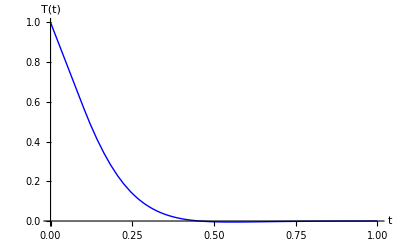

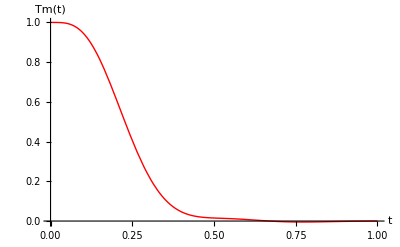

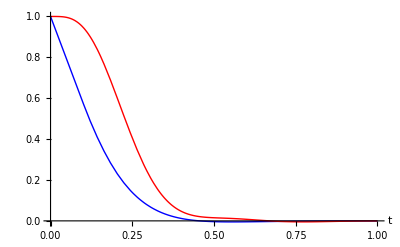

```mathematica
ClearAll;
a=1;
v=1;
k=2;
m=3;
τ=0.1;
γ=v^2/(4*a^2)+a^2*k^2;
γ*τ
ft[x_[t_]]:=γ*x[t];
f[x_[t_]]:=(*(τ^3/6)*x''''[t]+(τ^2/2)*x'''[t]+*)τ*x''[t]+x'[t]+ft[x[t]];
ff[x_[t_]]:=Sum[(τ^(n-1)/Factorial[n-1])*D[x[t],{t,n}],{n,m+1}]+ft[x[t]];
init:={};
upto:=1;
For[i=m,i≥1,i--,
PrependTo[init,(D[x[t],{t,i}]==0)/.{t->0}]
]
PrependTo[init,x[0]==1];
g[x_[t_]]:=x'[t]+ft[x[t-τ]];
sol1=NDSolve[{f[x[t]]==0,x[0]==1,x'[0]==0},x,{t,0,upto}];
sol2=NDSolve[{g[x[t]]==0,x[t/;t<0]==1},x,{t,0,upto}];
sol3=NDSolve[Join[{ff[x[t]]==0},init],x,{t,0,upto}];
p1:=Plot[Evaluate[x[t]/.sol1],{t,0,upto},PlotStyle->Red,PlotRange->All];
p2:=Plot[Evaluate[x[t]/.sol2],{t,0,upto},PlotStyle->Blue,PlotRange->All,AxesLabel->{"t","T(t)"}];
p3:=Plot[Evaluate[x[t]/.sol3],{t,0,upto},PlotStyle->Red,PlotRange->All,AxesLabel->{"t","Tm(t)"}];
(*Show[p1]*)
Show[p2]
Show[p3]
Show[{p2,p3},AxesLabel->{"t",""},PlotRange->All]
```